## Setting Up Equations

```mathematica
<< KerrGeodesics`
<< GeneralRelativityTensors`
Clear["Global`*"]
```

```mathematica
ClearAll;
M = 1;
Subscript[θ, inc]= π/1000;
Subscript[χ, inc] =-Cos[Subscript[θ, inc]];
a = 0.9999;
p = KerrGeoISSO[a,Subscript[χ, inc]];
L = KerrGeoAngularMomentum[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
Q = KerrGeoCarterConstant[a,KerrGeoISSO[a,Subscript[χ, inc]],0,Subscript[χ, inc] ];
ϵ =KerrGeoEnergy[a,p,0,Subscript[χ, inc] ];
J = 1-ϵ^2;
RM = M- Sqrt[M^2-a^2];
RP = M+ Sqrt[M^2-a^2];
RI = KerrGeoISSO[a,Subscript[χ, inc]]; (*Sqrt[(-a^2-L^2-Q+a^2 ϵ^2-√(12 a^2 Q (-3+3 ϵ^2)+(a^2+L^2+Q-a^2 ϵ^2)^2))/(6 (-1+ϵ^2))]*)
R4 =(a^2 Q)/(J*RI^3) ;
Z1=Sqrt[1/2 (1+L^2/(a^2 (1-ϵ^2))+Q/(a^2 (1-ϵ^2))-√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-L^2/(a^2 (1-ϵ^2))-Q/(a^2 (1-ϵ^2)))^2))];
Z2 =Sqrt[ (a^2(1-ϵ^2))/2 (1+L^2/(a^2 (1-ϵ^2))+Q/(a^2 (1-ϵ^2))+√(-(4 Q)/(a^2 (1-ϵ^2))+(-1-L^2/(a^2 (1-ϵ^2))-Q/(a^2 (1-ϵ^2)))^2))];
KZ = a^2*J(Z1^2/Z2^2);
```

### λ of R equation

```mathematica
Mino[r_]:=(2 √(r-R4))/(√(J (RI-r) (R4-RI)^2));
(*Solve[-3 R+3 R ϵ^2-(3 a^2 Q)/(R (1-ϵ^2))+(3 a^2 Q ϵ^2)/(R (1-ϵ^2))==-a^2-Q+4 a ϵ+2 a^2 ϵ^2-(2+a ϵ)^2,R];*)
```

### Radial Equation

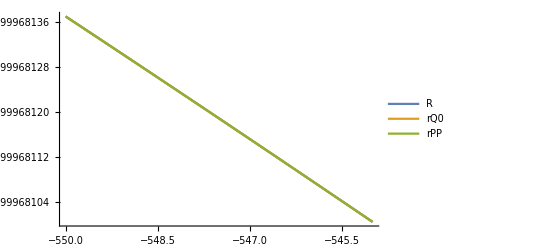

```mathematica
r[λ_]:=((RI(RI-R4)^2 J*λ^2+4*R4)/((RI-R4)^2 J*λ^2+4));
rQ0[λ_]:= (J RI^3 λ^2)/(4+J RI^2 λ^2);
rPP[λ_]:=(J RI^3 λ^2)/(4+J RI^2 λ^2)-(4 (a^2 (-4+J RI^2 λ^2)) Q)/(J RI^3 (4+J RI^2 λ^2)^2);

Plot[{r[λ],rQ0[λ],rPP[λ]},{λ,-550,-545},PlotLegends->{R,rQ0,rPP}]
```

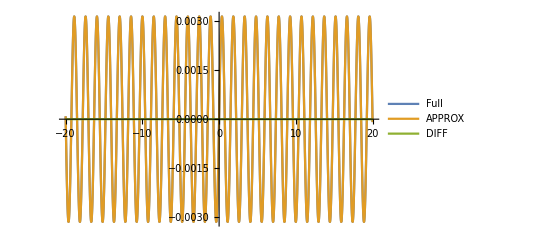

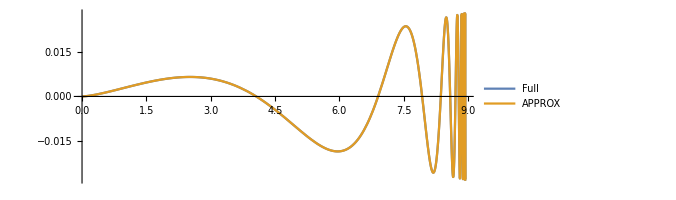

```mathematica
ΥZ = (π*Z2)/(2*EllipticK[KZ]);
qZ[λ_]:= ΥZ*λ 
z[λ_] := Z1*JacobiSN[EllipticK[KZ]*2(ΥZ*λ )/π,KZ] ;
θ[λ_] := ArcCos[Z1*JacobiSN[EllipticK[KZ]*2(ΥZ*λ )/π,KZ]];
zQ[λ_] := Z1*Sin[Z2 λ];
θQ[λ_] := ArcCos[Z1*Sin[Z2 λ]];
PolyZ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{z[λ],zQ[λ],z[λ]-zQ[λ]},{λ,-20,20},PlotLegends->{Full,APPROX,DIFF}]

ParametricPlot[{{r[λ]*Cos[π/2-θ[λ]],r[λ]*Sin[π/2-θ[λ]]},{r[λ]*Cos[π/2-θQ[λ]],r[λ]*Sin[π/2-θQ[λ]]}}, {λ,0,10}, PlotRange->All,PlotLegends->{Full,APPROX}]
```

### Azimuthal Equation

```mathematica
(*Integrate[(a(ϵ(r^2+a^2)-a*L))/((r-RP)(r-RM))(1/(Sqrt[J](RI-r)^(3/2)(r-R4)^(1/2))), r]*)
```

```mathematica
Υϕ =   L/EllipticK[KZ] EllipticPi[Z1^2, KZ];
qϕ[λ_] := Υϕ*λ + π/2;

Subscript[ϕ, r][λ_]:=1/(√J)2 a ((λ (RI-R4)√J (-a L+a^2 ϵ+RI^2 ϵ))/(2(-R4+RI) (RI-RM) (RI-RP))+((-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(2  √(RM-R4))/(λ (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP))+((-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(2  √(RP-R4))/(λ (RI-R4)√J √(RI-RP))])/(√(RP-R4) (RI-RP)^(3/2) (RM-RP))) ;
Subscript[ϕ, θ][λ_] :=L/Z2 EllipticPi[Z1^2,JacobiAmplitude[EllipticK[KZ]*2(ΥZ*λ + π/2)/π,KZ],KZ]-L/Z2 EllipticPi[Z1^2,JacobiAmplitude[EllipticK[KZ]*2(π/2)/π,KZ],KZ];

ϕ[λ_] := Subscript[ϕ, r][λ]+ Subscript[ϕ, θ][λ] -a*ϵ*λ

ϕQ[λ_] := Subscript[ϕ, r][λ]+ λ*L -a*ϵ*λ
```

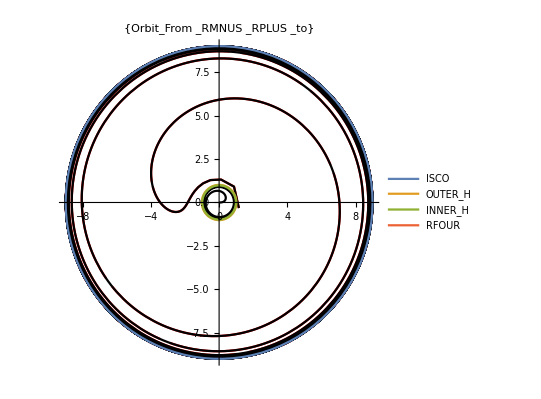

```mathematica
Q1 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Sin[Re[ϕ[λ]]]}, {λ,Mino[RP]+0.03,30}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Red, PlotLegends->ORBIT];
Q2 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕQ[λ]]],-Re[r[λ]]*Sin[Re[ϕQ[λ]]]}, { λ,Mino[RM]+0.05,Mino[RP]-0.5}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Black, PlotLegends->ORBITQ];
Q25 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕQ[λ]]],Re[r[λ]]*Sin[Re[ϕQ[λ]]]}, {λ,Mino[RP]+0.03,30}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Black, PlotLegends->ORBITQ];
Q3 = ParametricPlot[{Re[r[λ]]*Cos[Re[ϕQ[λ]]],Re[r[λ]]*Sin[Re[ϕQ[λ]]]}, {λ,0,Mino[RM]-0.005}, PlotRange->All, PlotLabel->{Orbit_From_RPLUS_to_RMNUS}, PlotStyle->Black, PlotLegends->ORBITQ];
Q4 = ParametricPlot[{{RI*Cos[u],RI Sin[u]},{RP*Cos[u],RP Sin[u]},{RM*Cos[u],RM Sin[u]},{R4*Cos[u],R4 Sin[u]}},{u,-π,π},MaxRecursion->1,PlotRange->All,PlotLegends->{ISCO,OUTER_H,INNER_H,RFOUR}];

Show[Q1,Q25,Q3,Q4]
```

### 3D plots

### (*,Specularity[White,1000]*)

```mathematica
P1 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,0,15}, PlotStyle->Red,PlotRange->All];

P2 = ParametricPlot3D[{Re[r[λ]]*Sin[Re[ϕQ[λ]]]*Sin[Re[θ[λ]]],Re[r[λ]]*Sin[Re[θ[λ]]]*Cos[Re[ϕQ[λ]]],Re[r[λ]]*Cos[Re[θ[λ]]]},{λ,0,15}, PlotStyle->Black,PlotRange->All];

P4 =ParametricPlot3D[{RP*Sin[u] Sin[v],RP*Cos[u] Sin[v],RP*Cos[v]},{u,-π,π},{v,-π,π},MaxRecursion->4,PlotStyle->{Opacity[0.2],Black,Specularity[White,10]}, Lighting->"Neutral",Axes->None,Mesh->None,PlotRange->All];
Show[P1,P2,P4]
```

-Graphics3D-

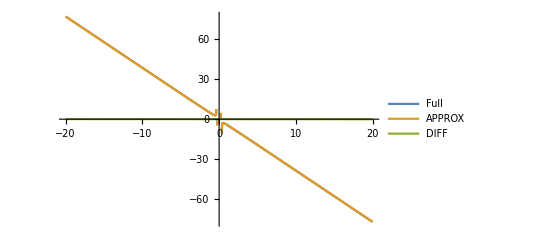

```mathematica
Plot[{ϕ[λ],ϕQ[λ],ϕ[λ]-ϕQ[λ]},{λ,-20,20},PlotLegends->{Full,APPROX,DIFF}]
```

### Time Function

#### Radial Part of time function

```mathematica
(*Clear[J,RI,R4,J,RM,RP]*)
```

```mathematica
Subscript[T, r][λ_]:= 1/(√J)(1/(2(-R4+RI) (RI-RM) (RI-RP)) λ(RI-R4)√J(-2 a^3 L-2 a L RI^2+2 a^4 ϵ+4 a^2 RI^2 ϵ+((RI(RI-R4)^2 J*λ^2+4*R4)/((RI-R4)^2 J*λ^2+4))(R4-RI) (RI-RM) (RI-RP) ϵ+RI (-R4 (RI-RM) (RI-RP)+RI (3 RI^2+RM RP-RI (RM+RP))) ϵ)-(R4+3 RI+2 (RM+RP)) ϵ ArcTan[(λ (RI-R4)√J)/2]+(2 (a^2+RM^2) (-a L+a^2 ϵ+RM^2 ϵ) ArcTanh[(2  √(RM-R4))/(λ (RI-R4)√J √(RI-RM))])/(√(RM-R4) (RI-RM)^(3/2) (-RM+RP))+(2 (a^2+RP^2) (-a L+a^2 ϵ+RP^2 ϵ) ArcTanh[(2  √(RP-R4))/(λ (RI-R4)√J √(RI-RP))])/(√(RP-R4) (RI-RP)^(3/2) (RM-RP))) ;


(*TPolyR[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)
Plot[{Subscript[T, r]'[λ],TPolyR[λ],Subscript[T, r]'[λ]-TPolyR[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}] - Must Change the branch we pick in negative time*)
```

#### ϕ part of time function

```mathematica
(*Clear["Global`*"]*)
```

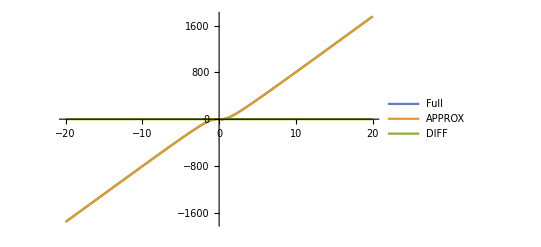

```mathematica
(*tTildeϕ[ξ_] = -ϵ/(1-ϵ^2)Z2*EllipticE[ξ, KZ];*)

Subscript[T, z][λ_]:=-1/J ϵ  (-Z2 EllipticE[JacobiAmplitude[-EllipticK[KZ]*2(ΥZ*λ + π/2)/π,KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[-JacobiAmplitude[EllipticK[KZ]*2(ΥZ*λ + π/2)/π,KZ],KZ])+(ϵ  (-Z2 EllipticE[JacobiAmplitude[-EllipticK[KZ]*2( π/2)/π,KZ],KZ]+(Z2-a^2 J/Z2) EllipticF[-JacobiAmplitude[EllipticK[KZ]*2(  π/2)/π,KZ],KZ]))/J
T[λ_]:= Subscript[T, r][λ]+Subscript[T, z][λ]+a*L*λ
TQ[λ_]:= Subscript[T, r][λ]-a^2 ϵ λ+a*L*λ

Plot[{T[λ],TQ[λ],T[λ]-TQ[λ]},{λ,-20,20},PlotLegends->{Full,APPROX,DIFF}]
```

### Mino Time in terms of Proper Time

```mathematica
EllipticF[n,0]
```

n

```mathematica
Simplify[Integrate[r^2/(Sqrt[J](RI-r)^(3/2)(r-R4)^(1/2)), r]];
```

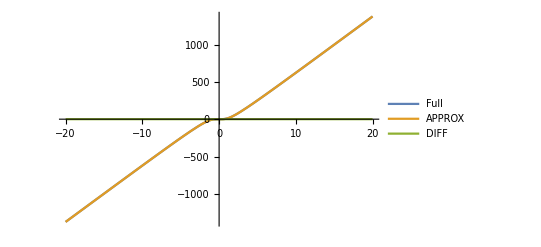

```mathematica
Subscript[τ, λr][λ_] :=((λ (RI-R4)√J(((RI(RI-R4)^2 J*λ^2+4*R4)/((RI-R4)^2 J*λ^2+4)) (R4-RI)+RI (-R4+3 RI)))/2+(R4^2+2 R4 RI-3 RI^2) ArcTan[λ (RI-R4)(√J)/2])/(√J (-R4+RI))
Subscript[τ, λz][λ_] :=(Z2  (EllipticE[- JacobiAmplitude[EllipticK[KZ]*2(ΥZ*λ + π/2)/π,KZ],KZ]-EllipticF[- JacobiAmplitude[EllipticK[KZ]*2(ΥZ*λ + π/2)/π,KZ],KZ]))/J - (Z2  (EllipticE[- JacobiAmplitude[EllipticK[KZ]*2( π/2)/π,KZ],KZ]-EllipticF[- JacobiAmplitude[EllipticK[KZ]*2( π/2)/π,KZ],KZ]))/J 



τ[λ_]:= Subscript[τ, λz][λ]+Subscript[τ, λr][λ]
τQ[λ_]:=Subscript[τ, λr][λ]


Plot[{τ[λ],τQ[λ],τ[λ]-τQ[λ]},{λ,-20,20},PlotLegends->{Full,APPROX,DIFF}]
```

### Kruskal Coordinates

```mathematica
σP = (M*RP)/Sqrt[M^2-a^2];
σM = (M*RM)/Sqrt[M^2-a^2];
ν = σM/σP;


V[λ_] := Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]+T[λ])/(2 σP)];
U[λ_] := -Abs[r[λ]-RP]^(1/2)/Abs[r[λ]-RM]^(ν/2)Exp[(r[λ]-T[λ])/(2 σP)];
ParametricPlot[{Re[U[λ]],Re[V[λ]]},{λ,-3,3}];
```

```mathematica
Integrate[1/Sqrt[(r-R1)(r-R2)(r-R3)(r-R4)], r];
```

### Analysis

```mathematica
(*ListX = Range[20,200,0.01];

ListKP = θ''/@ListX;
Listθ = ϕ''/@ListX;

ListPlot[{Transpose[{ListX,ListKP}], Transpose[{ListX,Listθ}]}, Joined->True,PlotLegends->Automatic]

(*FourListKP = Re[Fourier[ListKP]];
FourListθ = Re[Fourier[Listθ]];

ListPlot[{Transpose[{ListX,FourListKP}],Transpose[{ListX,FourListθ}]}, Joined->True,PlotRange->{{20,200},{-0.11,.1}},PlotLegends->Automatic]*)


fB=1.0;
Data1=Table[ϕ''[x],{x,1900,2000,1/10}];
sra=10./1;
inco=sra/Length[Data1];
fresa=Table[f,{f,0,sra-inco,inco}];
fData=Transpose[{fresa,Flatten[Abs[Fourier[Data1]]]}];
peaks=fData[[FindPeaks[fData[[All,2]]][[All,1]]]];
ListPlot[fData,PlotRange->{Full,Full},Joined->True,Frame->True,FrameLabel->{Row[{Style["Frequency",FontSlant->Italic,FontSize->15]}],Row[{Style["Amplitude",FontSlant->Italic,FontSize->15]}]},LabelStyle->Blue,FrameTicksStyle->Directive[Orange,15],ImageSize->900,PlotStyle->{Red},Joined->True,AspectRatio->0.5,Epilog->{PointSize[0.003],Point[fData],Black,PointSize[.01],Point[peaks]},PlotLabel->"Peaks: "<>ToString[peaks]]

fB=1.0;
Data1=Table[θ''[x],{x,1900,2000,1/10}];
sra=10./1;
inco=sra/Length[Data1];
fresa=Table[f,{f,0,sra-inco,inco}];
fData=Transpose[{fresa,Flatten[Abs[Fourier[Data1]]]}];
peaks=fData[[FindPeaks[fData[[All,2]]][[All,1]]]];
ListPlot[fData,PlotRange->{Full,Full},Joined->True,Frame->True,FrameLabel->{Row[{Style["Frequency",FontSlant->Italic,FontSize->15]}],Row[{Style["Amplitude",FontSlant->Italic,FontSize->15]}]},LabelStyle->Blue,FrameTicksStyle->Directive[Orange,15],ImageSize->900,PlotStyle->{Red},Joined->True,AspectRatio->0.5,Epilog->{PointSize[0.003],Point[fData],Black,PointSize[.01],Point[peaks]},PlotLabel->"Peaks: "<>ToString[peaks]]*)
```

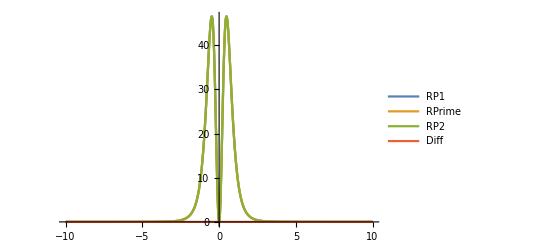

```mathematica
RPoly1[r_]:= (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q)

RPoly2[r_]:=J(RI-r)^3(r-R4)

Polyphir[r_]:= (a(ϵ(r^2+a^2)-a*L))/((r-RM)(r-RP));
Plot[{RPoly1[r[λ]], (r'[λ])^2, RPoly2[r[λ]], (r'[λ])^2- RPoly2[r[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,RP2,Diff},  PlotRange->All]
```

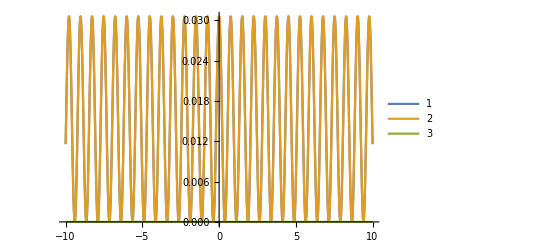

```mathematica
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2)
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},PlotRange->All]
```

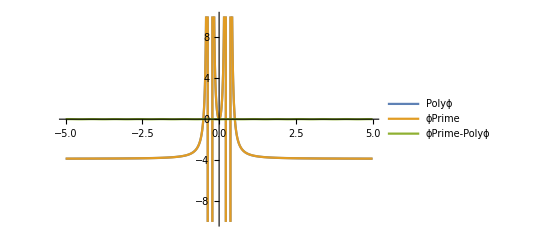

```mathematica
(*Plot[Im[ϕ[λ]],{λ,-5,5}]*)
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ
Plot[{Polyϕ[λ],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-5,5}, PlotRange->{{-5,5},{-10,10}},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ}]
```

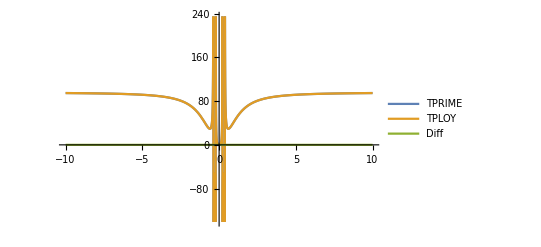

```mathematica
TPrime[λ_]:= Re[Piecewise[{{Subscript[T, r]'[λ]+Subscript[T, z]'[λ]+a*L,λ>0},{-Subscript[T, r]'[λ]+Subscript[T, z]'[λ]+a*L,λ<0}}]]
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L
Plot[{Re[T'[λ]],TPoly[λ],Re[T'[λ]]-TPoly[λ] },{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff}]
```

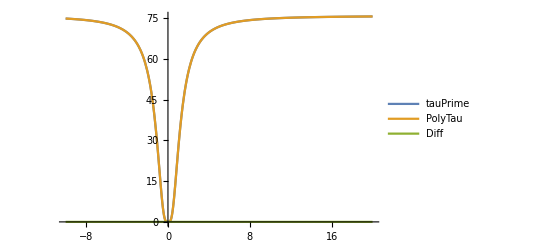

```mathematica
Plot[{τ'[λ],r[λ]^2+a^2 z[λ]^2,τ'[λ]-(r[λ]^2+a^2 z[λ]^2)},{λ,-10,20},PlotRange->All,{PlotLegends->{tauPrime,PolyTau,Diff}}]
```

### Checking the 4-Vector

```mathematica
(*Clear["Global`*"]*)
gKR = ToMetric["Kerr"];
TensorValues[gKR]//TableForm;

ModifiedKerr = {{-(1-2 r/(r^2+a^2 z^2)), 0, 0,(-2*a*r(1-z^2))/(r^2+a^2 z^2)}, {0,(r^2+a^2 z^2)/(r^2-2*M*r+a^2),0,0},{0, 0,(r^2+a^2 z^2)/(1-z^2),0} ,{ (-2*a*r(1-z^2))/(r^2+a^2 z^2),0,0,(1-z^2)/(r^2+a^2 z^2)(2*a^2*r(1-z^2)+(a^2+r^2)(r^2+a^2 z^2))}};
ModifiedKerr//MatrixForm;
gMKR = ToMetric[{"NewMetric", "g^MK"}, {t,r,z,ϕ}, ModifiedKerr, "Greek"];
```

Indices must be a list of Symbols (and negative Symbols).

Aborting in ToTensor[].

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {gKR}

$Aborted

Indices must be a list of Symbols (and negative Symbols).

Aborting in ToTensor[].

$Aborted

```mathematica
U1 = ToTensor[{"NewTensor", "U1"}, gMKR, {(r[λ]^2+a^2 z[λ]^2)^-1 T'[λ],(r[λ]^2+a^2 z[λ]^2)^-1 r'[λ],(r[λ]^2+a^2 z[λ]^2)^-1 z'[λ],(r[λ]^2+a^2 z[λ]^2)^-1 ϕ'[λ]}, {α}];
U2 = ToTensor[{"NewTensor", "U2"}, gMKR, { (r^2+a^2)/(r^2-2M*r+a^2)(ϵ(r^2+a^2)-a*L)-a^2 ϵ(1-z^2)+a*L,-( (ϵ(r^2+a^2)-a*L)^2-(r^2-2M*r+a^2)(r^2+(a*ϵ-L)^2+Q))^(1/2),(Q-(z^2(a^2(1-ϵ^2)(1-z)^2)+L^2-Q))^(1/2),a/(r^2-2M*r+a^2)(ϵ(r^2+a^2)-a*L) + L/(1-z^2)-a*ϵ}, {α}];
```

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,U1},gMKR,{(-3.74742+3.61553 (0.671496/((1-0.135795/λ^2) λ^2)-0.156217/((1-0.0476177/λ^2) λ^2)-34.9093/(1+1.45224 λ^2)+0.00233112 λ (-(50297.5 λ)/(4+5.80895 λ^2)+(5771.66 λ (0.00195599+50.6224 λ^2))/((4+5.80895 λ^2)^2))+0.00233112 (16227.2-(496.791 (0.00195599+50.6224 λ^2))/(4+5.80895 λ^2)))-12.5621 (-(17.3677 JacobiDN[1. (1.5708+4.17488 λ),6.23411×10^-6])/(√(1-6.23411×10^-6 Sin[1. JacobiAmplitude[1. (1.5708+4.17488 λ),6.23411×10^-6]]^2))+17.4297 JacobiDN[1.5708+4.17489 λ,6.23411×10^-6] √(1-6.23411×10^-6 Sin[1. JacobiAmplitude[1.5708+4.17489 λ,6.23411×10^-6]]^2)))/(((0.00195599+50.6224 λ^2)^2)/((4+5.80895 λ^2)^2)+0.00142039 JacobiSN[4.17489 λ,6.23411×10^-6]^2),((101.245 λ)/(4+5.80895 λ^2)-(11.6179 λ (0.00195599+50.6224 λ^2))/((4+5.80895 λ^2)^2))/(((0.00195599+50.6224 λ^2)^2)/((4+5.80895 λ^2)^2)+0.00142039 JacobiSN[4.17489 λ,6.23411×10^-6]^2),(0.174826 JacobiCN[4.17489 λ,6.23411×10^-6] JacobiDN[4.17489 λ,6.23411×10^-6])/(((0.00195599+50.6224 λ^2)^2)/((4+5.80895 λ^2)^2)+0.00142039 JacobiSN[4.17489 λ,6.23411×10^-6]^2),(-0.864891+6.50796 (0.180677+0.116913/((1-0.135795/λ^2) λ^2)-0.0692317/((1-0.0476177/λ^2) λ^2))-(4.1638 JacobiDN[1. (π/2+4.17488 λ),6.23411×10^-6])/((1-0.00175357 JacobiSN[1. (π/2+4.17488 λ),6.23411×10^-6]^2) √(1-6.23411×10^-6 JacobiSN[1. (π/2+4.17488 λ),6.23411×10^-6]^2)))/(((0.00195599+50.6224 λ^2)^2)/((4+5.80895 λ^2)^2)+0.00142039 JacobiSN[4.17489 λ,6.23411×10^-6]^2)},{α}}

$Aborted

Invalid call to ToTensor[]. Unexpected parameters: {{NewTensor,U2},gMKR,{-3.74742+((0.81+r^2) (3.74742+0.96099 (0.81+r^2)))/(0.81-2 r+r^2)-0.778402 (1-z^2),-√(-((25.3183+r^2) (0.81-2 r+r^2))+(3.74742+0.96099 (0.81+r^2))^2),√(-17.2761-0.0619641 (1-z)^2 z^2),-0.864891+(0.9 (3.74742+0.96099 (0.81+r^2)))/(0.81-2 r+r^2)-4.1638/(1-z^2)},{α}}

$Aborted

```mathematica
U1[-t]
U2[-t];
```

U1[-t]

```mathematica
HH[λ_]:= ((-1+(2 r[λ])/(r[λ]^2+a^2 z[λ]^2)) T'[λ])/(r[λ]^2+a^2 z[λ]^2)-(2 a r[λ] (1-z[λ]^2) ϕ'[λ])/((r[λ]^2+a^2 z[λ]^2) (r[λ]^2+a^2 z[λ]^2))

HH[2]
```

-0.960997

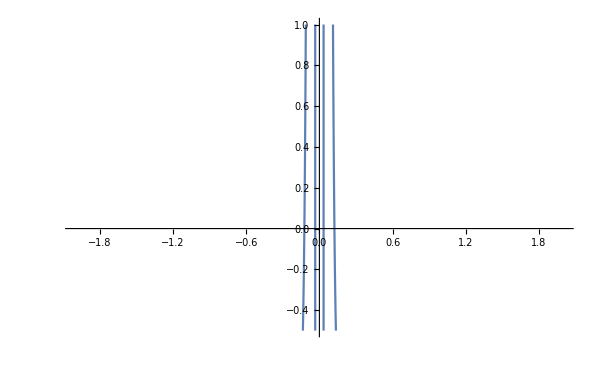

```mathematica
Plot[{Re[HH[λ+0.01*I]]}, {λ,-2,2},PlotRange->{{-2,2},{-0.5,1}}]
```

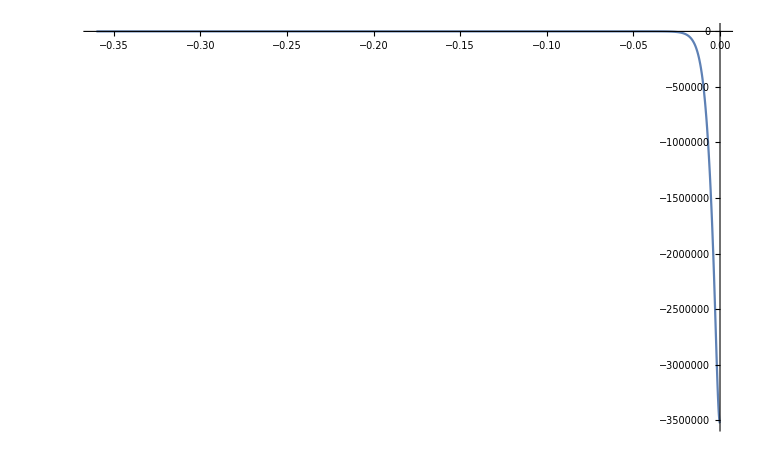

-0.96099

0.368504

```mathematica
Plot[{Re[HH[λ+0.01*I]]}, {λ,-0.36,0},PlotRange->All]
-ϵ
Mino[RP]
```